```mathematica
(* redefining Wald CI for convenience *) 
interWald[jj_, nn_,confLvl_]:=With[{t025=Quantile[NormalDistribution[],1 - (1-confLvl)/2]},Interval[Max[0,#]&/@{jj/nn -t025  √(jj/nn (1-jj/nn)/nn),jj/nn +t025  √(jj/nn (1-jj/nn)/nn)}]];

(* redefining Wilson CI for convenience *) 
interWilson[jj_, nn_,confLvl_]:=With[{t025=Quantile[NormalDistribution[],1 - (1-confLvl)/2]}, Interval[{1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2-t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2))),1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2+t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2)))}]];
```

```mathematica
Clear[dataDirPathSesh4, dataDirPathSesh5,monFilenames,  allMonFilenames, detFilenames, allDetFilenames, iterationDirName, countFromFiles]

(*** SESSION-SPECIFIC HACKS ***) 

(* hardcoded paths *) 
(*dataDirPathSesh4 = "~/Dropbox/upenn/research/aa/monitoring_data/data/Session_4_Sonar_Nocontroller_8Aug2019/";
dataDirPathSesh5 = "~/Dropbox/upenn/research/aa/monitoring_data/data/Session_5_Sonar_Nocontroller_9Sept_2019/";
dataDirPathSesh6 = "~/Dropbox/upenn/research/aa/monitoring_data/data/Session_6_Sonar_Nocontroller_23Sept_2019/";*)

(* session number -> data directory for it *) 
dataDirPathForSeshNum[seshNum_]:= Switch[seshNum, 4, "~/Dropbox/upenn/research/aa/monitoring_data/data/Session_4_Sonar_Nocontroller_8Aug2019/", 5,"~/Dropbox/upenn/research/aa/monitoring_data/data/Session_5_Sonar_Nocontroller_9Sept_2019/",6,"~/Dropbox/upenn/research/aa/monitoring_data/data/Session_6_Sonar_Nocontroller_23Sept_2019/",
 _ , Throw[StringJoin["Unknown session number: ", ToString[seshNum]] ]];

(* a hack to determine different spellings of Iteration_1 or Iteration1, given session info *)
iterationDirName[seshNum_]:= If[seshNum == 4, "Iteration_", "Iteration"];

(* a hack to determine complete pairlists for each session; the triples are (seshnum, iternum, detnum) *)
fullTripleList[seshNums_]:= Flatten[Switch[#, 4,(* for session 4 *) Join[{4}, #]& /@Flatten[Outer[List, Range[1,5], Range[1,5]], 1], 5,(* for session 5 *)Join[{5}, #]& /@ Flatten[Outer[List, Range[1,5],{1}], 1],6,(* for session 6 *)Join[{6}, #]& /@ Flatten[Outer[List, Range[1,24],{1}], 1],
 _, {}]& /@ seshNums, 1];

fullTripleListNoRedun[seshNums_]:= Flatten[Switch[#, 4,(* for session 4 *) Join[{4}, #]& /@Flatten[Outer[List, Range[1,5],{1}], 1], 5,(* for session 5 *)Join[{5}, #]& /@ Flatten[Outer[List, Range[1,5],{1}], 1],6,(* for session 6 *)Join[{6}, #]& /@ Flatten[Outer[List, Range[1,24],{1}], 1], _, {}]& /@ seshNums, 1];


(*** FILE MANIPULATIONS ***)

monFilenames[idtriplelist_, winSize_] := StringJoin[dataDirPathForSeshNum@#[[1]],iterationDirName[#[[1]]], ToString[#[[2]]], "/mon", ToString[#[[3]]], "_",ToString[winSize], "/iter", ToString[#[[2]]], "_mondet", ToString[#[[3]]], "_",ToString@winSize, "_estrates.txt"] & /@idtriplelist;

detFilenames[idtriplelist_] := StringJoin[dataDirPathForSeshNum@#[[1]],iterationDirName[#[[1]]], ToString[#[[2]]], "/det", ToString[#[[3]]], "/iter", ToString[#[[2]]], "_both_det_estrates.txt"] & /@idtriplelist;

allMonFilenames[seshNums_, winSize_] := Flatten[monFilenames[fullTripleList[{#}], winSize] & /@ seshNums];

allDetFilenames[seshNums_] := Flatten[detFilenames[fullTripleList[{#}]] & /@ seshNums];


(* add up a given field's values over filenames *) 
countFromFiles[fieldName_, filenames_] := Plus@@(*list of frame numbers from each*)(getValueFromListOfPairs[#,fieldName]& /@ (*list of all stat dicts*) (nameValuePairsFromFile/@filenames(*list of filenames*)))
```

```mathematica
(* various counts from mons, for sanity *) 
allMonH1ct = countFromFiles[ "h1count",allMonFilenames[{4,5,6},10]]
allMonFNct = countFromFiles[ "FNcount",allMonFilenames[{4,5,6},10]]
allDetH0ct =countFromFiles[ "h0count",allDetFilenames[{4,5,6}]]
allDetFPct =countFromFiles[ "FPcount",allDetFilenames[{4,5,6}]]
```

1211

817

1984

200

```mathematica
(* PREDICTIONS basics *) 
Clear[predFNR, chart95conf,subsetCt,allSubsetCt]

predFNR[detFPR_, monWin_, pDetNCH0_:0(* for this context *)] := 1 - (1-detFPR)(1 - detFPR - pDetNCH0)^(monWin-1);

chart95conf[maxSampleSize_] := ListLinePlot[Inner[List, Range[0,maxSampleSize],Table[0.95, maxSampleSize+1], List], PlotStyle->{Red, Dotted}];(*ListLinePlot[Table[0.95, 25], PlotStyle->{Red, Dotted}];*)

(* number of subsets excluding the empty one *) 
subsetCt[set_] := 2^(Length@set)-1;
subsetCtOfSize[set_, subsetSize_]:= Binomial[Length@set, subsetSize];
allSubsetCt = subsetCt@fullTripleList[{4,5}];
```

```mathematica
(*** DATA ANALYSIS ***)
Clear[pairingPredMonFNR, oneIntervalTestGeneral, generateBinarySampleNonRepl,tallyUpBinarySample, generateCIRSOutcomesGeneral]

(** Pairings **)
(* returns basic pairing between interval and prediction point: (interval from data, prediction/gt) *)

(* TODO: factor out monitor win size as a parameter to something else *) 

(* for predicted monitor FNR *)
pairingPredMonFNR[tripleIdList_,monWinSize_, intervalType_: interWald, confidence_:0.95] := {(* interval *) intervalType[countFromFiles[ "FNcount",monFilenames[tripleIdList, monWinSize ]], countFromFiles[ "h1count",monFilenames[tripleIdList, monWinSize ]], confidence], (* prediction *) predFNR[countFromFiles[ "FPcount",detFilenames@tripleIdList]/countFromFiles[ "h0count",detFilenames@tripleIdList], monWinSize]};

(* for detector GT FPR *) 
pairingGtDetFPR[tripleIdList_,monWinSize_(*not used*), intervalType_: interWald, confidence_:0.95] := {(* interval *) intervalType[countFromFiles[ "FPcount",detFilenames[tripleIdList ]], countFromFiles[ "h0count",detFilenames[tripleIdList ]], confidence], (* ground truth *) 0.1};

(* for detector GT FNR *) 
pairingGtDetFNR[tripleIdList_,monWinSize_(*not used*), intervalType_: interWald, confidence_:0.95] := {(* interval *) intervalType[countFromFiles[ "FNcount",detFilenames[tripleIdList ]], countFromFiles[ "h1count",detFilenames[tripleIdList ]], confidence], (* ground truth *) 0.1};


(* generates a true/false response for intervals containing things in pairs, for a particular pairing function *) 
oneIntervalTestGeneral[pairingFn_,tripleIdList_,monWinSize_,  intervalType_:interWald, confidence_:0.95 ] := 
With[{testPair = pairingFn[tripleIdList,monWinSize,intervalType, confidence]}, IntervalMemberQ[testPair[[1]], testPair[[2]]]];


(*** IMPLEMENTATIONS OF SAMPLING ***) 

(** Option 1a: Randomized NON-REPLACEMENT sampling across all subsets **) 
Clear[generateBinarySampleNonRepl, tallyUpBinarySample,generateCIRSOutcomesGeneral];

(* returns a list of pairs {subset size used, whether CI contains the prediciton}. Can do tripling if needed *) 
generateBinarySampleNonRepl[pairingFn_, seshNums_, totalSampleCt_, monWinSize_, intervalType_:interWald, confidence_:0.95, testFn_:oneIntervalTestGeneral]:= With[{tripleList =fullTripleList[seshNums] },({#[[1]],testFn[pairingFn, #[[2]],monWinSize, intervalType, confidence]}&/@( Flatten[{Length@#, #} &/@(* list of lists of subsets of possible sets of pairs for tests.
aka: {   {subsetsize, triplelist}, {subsetsize, triplelist, ...}   } *) Subsets[tripleList,{1, Length@tripleList},{#}] &/@ (* getting random subsets *)  RandomInteger[{1,(*all subsets *)subsetCt[tripleList]
},totalSampleCt],1]))];

(* Represents trues and falses as counts, in triples of {subsetsize, # of trues at that size, # of falses at that size}.
Takes in a list of pairs {subset size, true/false} *)
tallyUpBinarySample[sample_, maxSubsetSize_]:= With[ {trueCt= Count[sample, {#, True}], falseCt= Count[sample, {#, False}]} , {#,trueCt, falseCt}]& /@  Range[1,maxSubsetSize];

(* Evaluation of CI via random NON-REPLACEMENT sampling  across all subsets, producing outcome pairs {subset size, accuracy w/uncert based on wilson CIs}, by converting tallied triples to ratios and stdev *) 
generateCIRSOutcomesGeneral[pairingFn_, seshNums_, sampleCt_, monWinSize_, intervalTypeForEstim_:interWald, intervalTypeForEval_:interWald,confidence_:0.95, testFn_:oneIntervalTestGeneral]:={(*subset size*) #[[1]], (*ratio of successes to total *) With[{est = #[[2]]/(#[[2]]+#[[3]]), int = intervalTypeForEval[#[[2]],#[[2]]+#[[3]], 0.95]},Around[(*estimated accuracy*)est,(* converting wilson interval to uncertainty bounds*) {Min@int-est, Max@int-est}]] }&/@ (* getting tallied sample data and filtering it*)Select[tallyUpBinarySample[generateBinarySampleNonRepl[pairingFn, seshNums, sampleCt,monWinSize, intervalTypeForEstim,confidence, testFn], Length@fullTripleList@seshNums], #[[2]] >0 ∨ #[[3]]>0 # &];

(** Option 1b: Fixed subsets **) 
Clear[generateSuccessCtsPerSubsetSize,  generateSuccessCtsPerSubsetSizeForCharting, generateCIOutcomesPerSubsetSize];

(* sample success counts fixed per subset size *) 
generateSuccessCtsPerSubsetSize[pairingFn_, triplingFn_, seshNums_, monWinSize_, samplesPerSubsetSize_, intervalType_:interWald, confidence_:0.95,testFn_:oneIntervalTestGeneral]  := With[{subsetsCt = #},
(* count truths *)Count[ (* apply test function, get T/F *) testFn[pairingFn, #, monWinSize, intervalType, confidence]&/@ (* all possible sets of pairs for tests *) Subsets[triplingFn@seshNums, {subsetsCt},{#}] &/@ (* getting samplesPerSubsetSize random subsets *)  RandomInteger[{1,(*counting subsets *)subsetCtOfSize[triplingFn@seshNums, subsetsCt]
},samplesPerSubsetSize], {True}]
]& /@ (* iterating through subset sizes *) Range[1, Length@triplingFn@seshNums];

(* adds lengths to each count and divides it by the length *)
generateSuccessCtsPerSubsetSizeForCharting[pairingFn_, triplingFn_, seshNums_, monWinSize_, samplesPerSubsetSize_, intervalType_:interWald, confidence_:0.95,testFn_:oneIntervalTestGeneral] := With[{successCts = generateSuccessCtsPerSubsetSize[pairingFn,triplingFn, seshNums, monWinSize, samplesPerSubsetSize, intervalType, confidence,testFn]},Inner[List,Range[1,Length@successCts], successCts/samplesPerSubsetSize, List]];

(* generates confidence intervals out of the above success counts *) 
generateCIOutcomesPerSubsetSize[pairingFn_,triplingFn_, seshNums_, monWinSize_, sampleCtPerSubsetSize_,intervalTypeForEstim_:interWald, intervalTypeForEval_:interWald,confidence_:0.95, testFn_:oneIntervalTestGeneral]:= Inner[List, Range[1,Length@triplingFn@seshNums], #, List]& @(With[{est = #/ sampleCtPerSubsetSize, int = intervalTypeForEval[#, sampleCtPerSubsetSize, confidence ]}, Around[(*estimated accuracy*)est,(* converting interval to uncertainty bounds for charts*) {Min@int-est, Max@int-est}]] &/@generateSuccessCtsPerSubsetSize[pairingFn,triplingFn, seshNums, monWinSize, sampleCtPerSubsetSize, intervalTypeForEstim,confidence, testFn] );


(** Option 2: Randomized (with REPLACEMENT) sampling across subsets **) 
Clear[getRandomTriple, getRandomTripleListWithRepl, generateTestedSampleRepl, generateReplSamplesForCharting];

(* get a random trace *) 
getRandomTriple[seshNums_] := With[{triples = fullTripleList[seshNums]},triples[[RandomInteger[{1,Length@triples}]]]];

(* get random subset of traces with replacement *)
getRandomTripleListWithRepl[seshNums_, size_]:= Table[getRandomTriple[seshNums], size];

(* generates a number of true attempts out of sampleCt *)
generateTestedSampleRepl[pairingFn_, seshNums_, traceCtInSample_, sampleCt_, monWinSize_, intervalType_:interWald, confidence_:0.95, testFn_:oneIntervalTestGeneral]:= Count[True]@(testFn[pairingFn, #,monWinSize, intervalType, confidence]&/@ (* get a triple at a time *)
Table[getRandomTripleListWithRepl[seshNums, traceCtInSample], sampleCt]);

(* generate samples across all trace counts *)
generateReplSamplesForCharting[pairingFn_, seshNums_,  maxTraceCtInSample_, sampleCt_, monWinSize_, intervalTypeForEstim_:interWald,intervalTypeForEval_:interWald, confidence_:0.95, testFn_:oneIntervalTestGeneral]:= 
{(*size of sample*) #[[1]], (*ratio of successes to total *) With[{est = #[[2]]/sampleCt, int = intervalTypeForEval[#[[2]],sampleCt, confidence]},Around[(*estimated accuracy*)est,(* converting wilson interval to uncertainty bounds*) {Min@int-est, Max@int-est}]] }&/@ 
(* list of (trace count, number of successes out of sampleCt) *) 
({#, generateTestedSampleRepl[pairingFn,seshNums,(*trace ct in sample*)#, sampleCt, 10]}&/@Range[1,  maxTraceCtInSample] );

(* getting tallied sample data and filtering it*)(*Select[tallyUpBinarySample[generateBinarySampleNonRepl[pairingFn, seshNums, sampleCt,monWinSize, intervalTypeForEstim,confidence, testFn], Length@fullTripleList@seshNums], #[[2]] >0 ∨ #[[3]]>0 # &]*)
```

```mathematica
(** Option 3: splitting into completely independent, disjoint subsets and testing each **)

(* generates a partition of triples and tries each as a binary test *)
generatePartitionSample[pairingFn_, seshNums_, partitionSize_, monWinSize_, intervalType_:interWald, confidence_:0.95, testFn_:oneIntervalTestGeneral]:= With[{tripleList =fullTripleList[seshNums] },testFn[pairingFn, #,monWinSize, intervalType, confidence] &/@ Partition[tripleList,partitionSize]];

generatePartitionOutcomesForCharting[pairingFn_, seshNums_, maxPartitionSize_, monWinSize_, intervalTypeForEstim_:interWald, intervalTypeForEval_:interWald, confidence_:0.95, testFn_:oneIntervalTestGeneral] :=
{(*size of partition*) #[[1]], (*ratio of successes to total *) With[{est = #[[3]]/#[[2]], int = intervalTypeForEval[#[[3]],#[[2]], confidence]},Around[(*estimated accuracy*)est,(* converting wilson interval to uncertainty bounds*) {Min@int-est, Max@int-est}]] }&/@ 
(* list of (partition size, number of successes) *) 
(With[{binarySample = generatePartitionSample[pairingFn,   seshNums, #, monWinSize]}, {#, Length@binarySample, Count[binarySample, True]} ]&/@  Range[1, maxPartitionSize]  );

(*( Flatten[{Length@#, #} &/@(* list of lists of subsets of possible sets of pairs for tests.
aka: {   {subsetsize, triplelist}, {subsetsize, triplelist, ...}   } *) Subsets[tripleList,{1, Length@tripleList},{#}] &/@ (* getting random subsets *)  RandomInteger[{1,(*all subsets *)subsetCt[tripleList]
},totalSampleCt],1]))];*)
```

```mathematica
(*** ACTUAL COMPUTATIONS ***)
(* get 100 lists of 100 samples like above *) 
Table[generateSuccessCtsPerSubsetSize[pairingPredMonFNR, 100, interWilson], 100]
```

```mathematica
reslists100 = ;
```

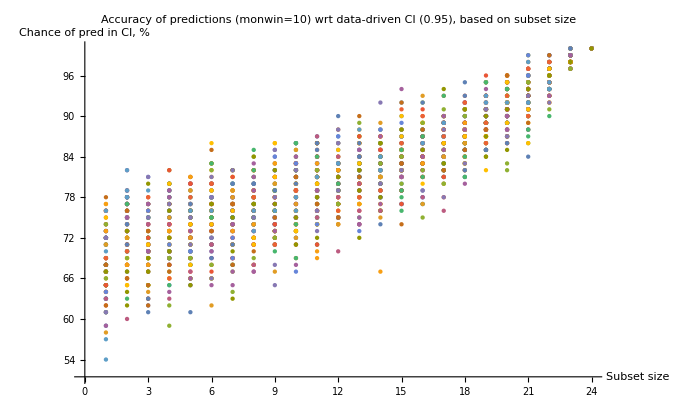

```mathematica
ListPlot[Inner[List, Range[1,24], #, List]& /@ reslists100, AxesLabel->{"Subset size", "Chance of pred in CI, %"}, PlotLabel->"Accuracy of predictions (monwin=10) wrt data-driven CI (0.95), based on subset size"]
```

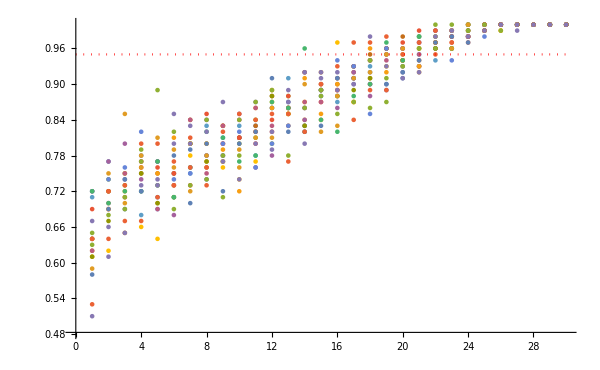
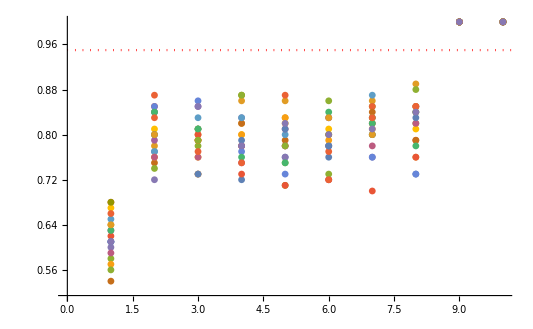
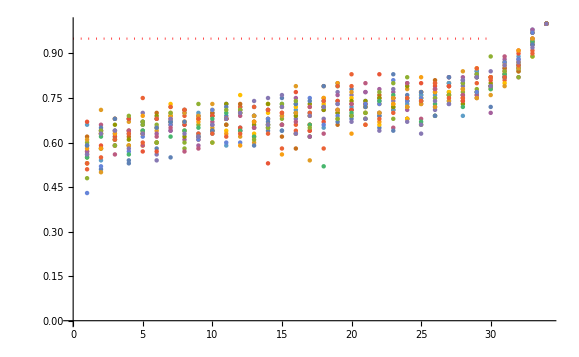
```mathematica
(* same as above but for sessions 4 and 5 *) 
Show[ListPlot@Table[generateSuccessCtsPerSubsetSizeForCharting[pairingPredMonFNR, {4,5}, (*monwin size, ignored in this case*) 10, (* attempts per dot *) 100],(* number of series *) 20],chart95conf[30]] 
-Graphics-

(* for non-redundant subsets *) 
Show[ListPlot@Table[generateSuccessCtsPerSubsetSizeForCharting[pairingPredMonFNR,fullTripleListNoRedun, {4,5}, (*monwin size, ignored in this case*) 10, (* attempts per dot *)100],(* number of series *) 20],chart95conf[30]] 
-Graphics-

(* same for session 6 *) 

Show[ListPlot@Table[generateSuccessCtsPerSubsetSizeForCharting[pairingPredMonFNR,fullTripleListNoRedun, {4,5,6}, (*monwin size*) 10, (* attempts per dot *)100],(* number of series *) 20],chart95conf[30]] 
-Graphics-


(* CIs for per-subset sampling*)
 generateCIOutcomesPerSubsetSize[pairingPredMonFNR,1000, interWilson, interWilson]
```

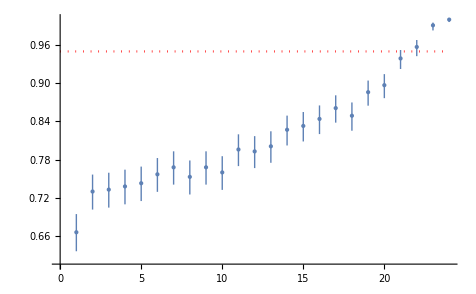

```mathematica
resestimates1000Wilson =;
(* clear dynamic here, despite small samples *) 
Show[ListPlot[resestimates1000Wilson, PlotStyle->PointSize[Large]], chart95conf]
```

```mathematica
generateCIOutcomesPerSubsetSize[pairingPredMonFNR,1000, interWald, interWald]
```

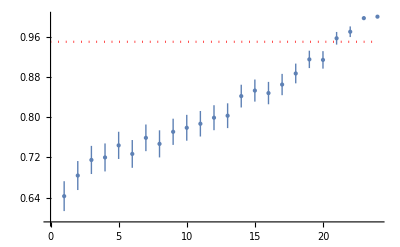

```mathematica
resestimates1000Wald = ;

Show[ListPlot[resestimates1000Wald, PlotStyle->PointSize[Large]], chart95conf]
```

```mathematica
(* larger sample, wilson *)
generateCIOutcomesPerSubsetSize[pairingPredMonFNR,10000, interWilson, interWilson]
```

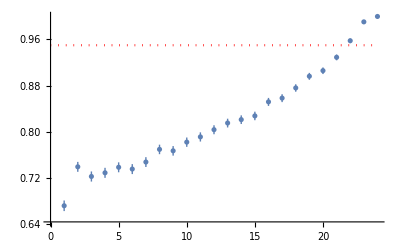

```mathematica
resestimates10000Wilson =;
Show[ListPlot[resestimates10000Wilson], chart95conf]
```

```mathematica
(* larger sample, wald *) 
generateCIOutcomesPerSubsetSize[pairingPredMonFNR,10000, interWald, interWald]
```

```mathematica
resestimates10000Wald = ;
Show[ListPlot[resestimates10000Wald, PlotStyle->PointSize[Medium]], chart95conf]
```

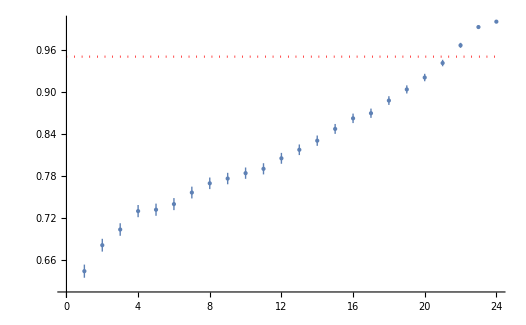

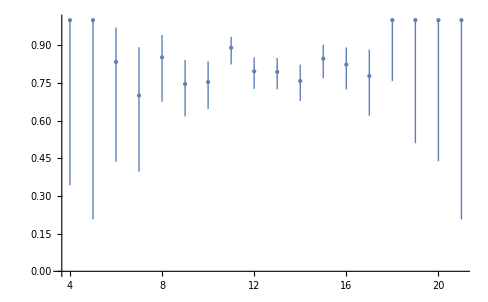

```mathematica
(* for random size sampling, WILSON: *)
(* 1000 samples, random, wilson *) 
ListPlot[generatePredvsCIOutcomes[1000], PlotStyle->PointSize[Large]]
```

```mathematica
(* 10k samples, random, wilson *) 
randomOutcomes10000= generatePredvsCIOutcomes[10000]
```

{{3,0.50.40.4},{4,0.570.320.27},{5,0.890.320.09},{6,0.690.120.10},{7,0.700.090.07},{8,0.760.050.04},{9,0.7640.040.032},{10,0.7630.0270.025},{11,0.7870.0230.021},{12,0.8110.0200.019},{13,0.8130.0210.019},{14,0.8160.0220.020},{15,0.8390.0240.022},{16,0.8270.0330.029},{17,0.8510.040.034},{18,0.880.060.04},{19,0.850.130.07},{20,0.800.310.14},{21,1.000000000000000000.40.00000000000000022}}

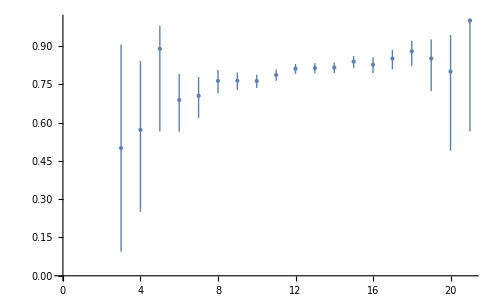

```mathematica
ListPlot[randomOutcomes10000, PlotStyle->PointSize[Large]]
```

```mathematica
(* 100k samples, random, wilson *) 
randomOutcomesWilson100000= generateMonFNRPredvsCIOutcomesWilson[100000]
```

{{3,0.570.320.27},{4,0.680.150.12},{5,0.710.070.06},{6,0.7470.040.035},{7,0.7300.0230.022},{8,0.7650.0150.014},{9,0.7740.0110.010},{10,0.7820.0080.008},{11,0.7920.0070.007},{12,0.7990.0060.006},{13,0.8070.0060.006},{14,0.8200.0070.006},{15,0.8370.0070.007},{16,0.8510.0090.009},{17,0.8570.0120.011},{18,0.8680.0190.017},{19,0.8720.0310.026},{20,0.910.050.04},{21,0.880.130.07},{22,1.000000000000000000.320.00000000000000022},{23,1.000000000000000000.60.00000000000000022}}

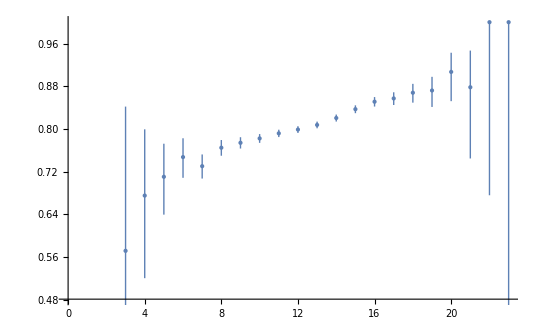

```mathematica
ListPlot[randomOutcomesWilson100000, PlotStyle->PointSize[Large]]
```

```mathematica
(* 100k samples, random,  WALD *) 
generateMonFNRPredvsCIOutcomesWald[100000]
```

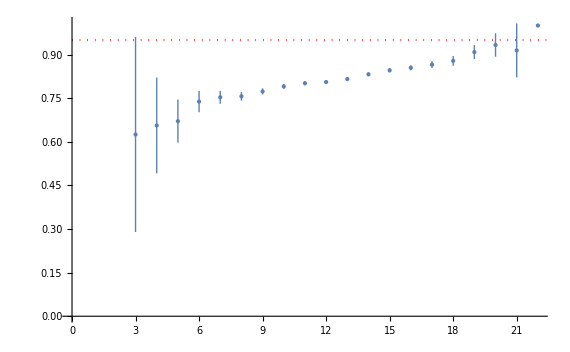

```mathematica
randomOutcomesWald100000 = ;
Show[ListPlot[randomOutcomesWald100000, PlotStyle->PointSize[Medium]], chart95conf]
```

```mathematica
(*** THREE-WAY COMPARISON: CI, Prediction for MonFNR, and GT for MonFNR 
it is a success if we either hit the interval or both we and GT miss it 
***) 

(* returns a triple {CI interval from data, predicted FNR, GT FNR} *)
triplingMonFNRCIPredGt[pairIdList_, intervalType_] := {(* interval *) intervalType[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *) predFNR[countFromFiles[ "FPcount",detFilenames[pairIdList]]/countFromFiles[ "h0count",detFilenames[pairIdList]], 10], (* GT of FNR *) predFNR[0.1, 10]};

(* returns false only if we missed the CI but the GT hit the CI *)
oneIntervalTripleTest[triplingFn_,pairIdList_, intervalType_] := 
With[{(*{CI,pred,GT}*) testTriple = triplingFn[pairIdList,intervalType]}, IntervalMemberQ[testTriple[[1]], testTriple[[2]]]∨¬IntervalMemberQ[testTriple[[1]], testTriple[[3]]] ];
```

```mathematica
(** THREE-WAY VISUALS FOR WILSON **) 

(* 100 samples per subset, that's not enough data *) 
generateCIOutcomesPerSubsetSize[triplingMonFNRCIPredGt, 100, interWilson, interWilson, oneIntervalTripleTest]
```

```mathematica
threewayPerSubset100 = ;
```

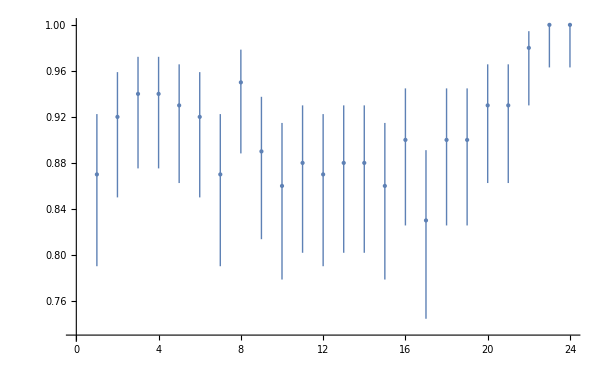

```mathematica
ListPlot[threewayPerSubset100, PlotStyle->PointSize[Large]]
```

```mathematica
(* 1k samples per subset *) 
generateCIOutcomesPerSubsetSize[triplingMonFNRCIPredGt, 1000, interWilson, interWilson, oneIntervalTripleTest]
```

```mathematica
threewayPerSubset1000 = ;
```

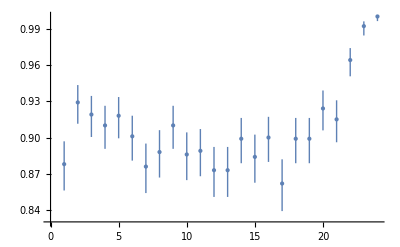

```mathematica
ListPlot[threewayPerSubset1000, PlotStyle->PointSize[Large]]
```

```mathematica
(* 10k samples per subset *)
generateCIOutcomesPerSubsetSize[triplingMonFNRCIPredGt, 10000, interWilson, interWilson, oneIntervalTripleTest]
```

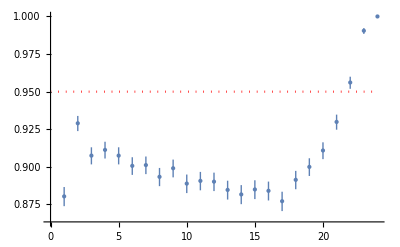

```mathematica
threewayPerSubset10000Wilson = ;
Show[ListPlot[threewayPerSubset10000Wilson, PlotStyle->PointSize[Medium]], chart95conf]
```

```mathematica
(* THREE-WAY VISUALS FOR WALD *) 
generateCIOutcomesPerSubsetSize[triplingMonFNRCIPredGt, 1000, interWald, interWald, oneIntervalTripleTest]
```

```mathematica
threewayPerSubset1000Wald = ;
```

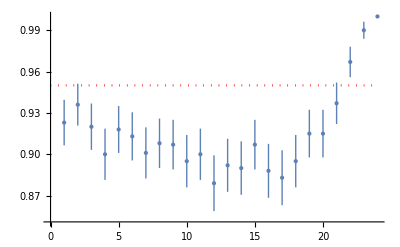

```mathematica
Show[ListPlot[threewayPerSubset1000Wald, PlotStyle->PointSize[Large]], chart95conf]
```

```mathematica
generateCIOutcomesPerSubsetSize[triplingMonFNRCIPredGt, 10000, interWald, interWald, oneIntervalTripleTest]
```

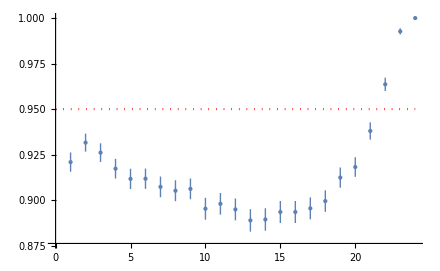

```mathematica
threewayPerSubset10000Wald = ;
(* depressing slope, weird *) 
Show[ListPlot[threewayPerSubset10000Wald, PlotStyle->PointSize[Medium]], chart95conf]
```

```mathematica
(*** TESTING WILSON CI FOR MONITOR FNR: data-driven Wilson CI for monitor FNR vs FNR ground truth ***) 
(* an outcome whether GT is in CI interval described by pairlist *) 

oneIntervalGtTestWilson[pairIdList_] := IntervalMemberQ[(* interval *) interWilson[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *) predFNR[0.1, 10]];

(* a pair of interval (described by pairlist) and GT *)
oneIntervalGtTestPairWilson[pairIdList_] := {(* interval *) interWilson[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *)  predFNR[0.1, 10]};
```

$Aborted

```mathematica
(* fixed subsets CI vs mon FNR GT *) 
generateGtSuccessCountsPerSubsetSizeWilson:= With[{subsetsCt = #},
(* count truths *)Count[oneIntervalGtTestWilson[#]&/@ (* all possible sets of pairs for tests *) Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt},{#}] &/@ (* getting random 100 subsets *)  RandomInteger[{1,(*counting subsets *)Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt}]
},100], {True}]
]& /@ Range[1, 24];
```

```mathematica
(* 100 runs of 100 samples each *) 
Table[generateGtSuccessCountsPerSubsetSizeWilson, 100]
```

```mathematica
resGtLists100Wilson =
```

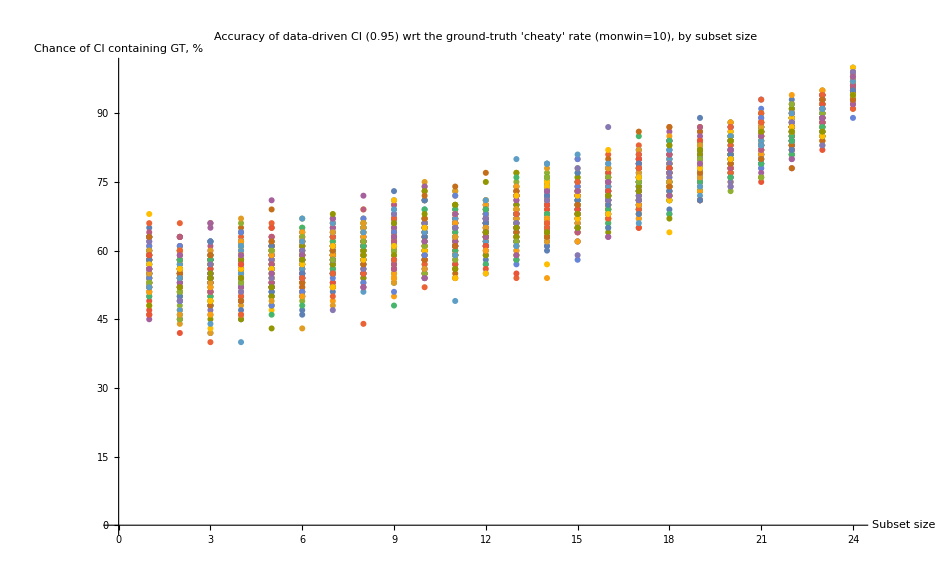

```mathematica
ListPlot[Inner[List, Range[1,24], #, List]& /@ resGtLists100Wilson, AxesLabel->{"Subset size", "Chance of CI containing GT, %"}, PlotLabel->"Accuracy of data-driven CI (0.95) wrt the ground-truth 'cheaty' rate (monwin=10), by subset size"]
```

```mathematica
(*** TESTING WALD CI FOR MONITOR FNR GT ***)
```

```mathematica
(* an outcome whether GT is in CI interval described by pairlist *) 

oneIntervalGtTestWald[pairIdList_] := IntervalMemberQ[(* interval *) interWald[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *) predFNR[0.1, 10]];

(* a pair of interval (described by pairlist) and GT *)
oneIntervalGtTestPairWald[pairIdList_] := {(* interval *) interWald[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *)  predFNR[0.1, 10]};
```

```mathematica
generateGtSuccessCountsPerSubsetSizeWald:= With[{subsetsCt = #},
(* count truths *)Count[oneIntervalGtTestWald[#]&/@ (* all possible sets of pairs for tests *) Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt},{#}] &/@ (* getting random 100 subsets *)  RandomInteger[{1,(*counting subsets *)Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt}]
},100], {True}]
]& /@ Range[1, 24];
```

```mathematica
(* 100 runs of 100 samples each *) 
Table[generateGtSuccessCountsPerSubsetSizeWald, 100]
```

```mathematica
resListsWald100 = ;
```

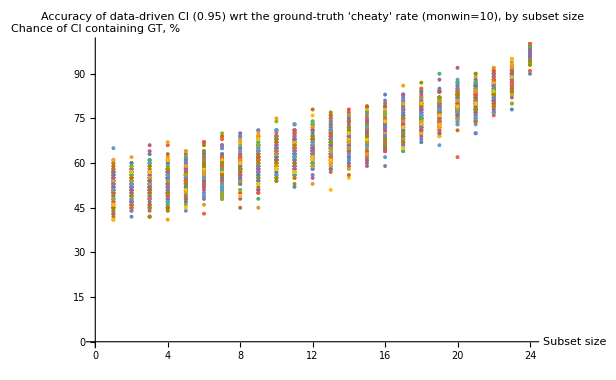

```mathematica
ListPlot[Inner[List, Range[1,24], #, List]& /@ resListsWald100a, AxesLabel->{"Subset size", "Chance of CI containing GT, %"}, PlotLabel->"Accuracy of data-driven CI (0.95) wrt the ground-truth 'cheaty' rate (monwin=10), by subset size"]
```

```mathematica
ListPlot[Inner[List, Range[1,24], #, List]& /@ resListsWald100b, AxesLabel->{"Subset size", "Chance of CI containing GT, %"}, PlotLabel->"Accuracy of data-driven CI (0.95) wrt the ground-truth 'cheaty' rate (monwin=10), by subset size"]
```

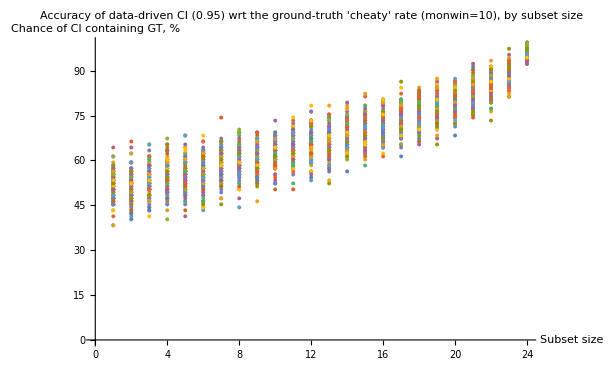

```mathematica
(** randomized sampling for wald CI vs ground truth monitor FNR **)
```

```mathematica
(* a list of pairs {subset size, whether CI contains the prediciton} *) 
generateMonGtFNRvsCISample[sampleCt_]:= ({#[[1]],oneIntervalGtTestWald[#[[2]]]}&/@( Flatten[{Length@#, #} &/@(* list of lists of subsets possible sets of pairs for tests *) Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {1,25},{#}] &/@ (* getting random 100 subsets *)  RandomInteger[{1,(*all subsets *)subsetCt
},sampleCt],1]));


(* converting tallied triples to ratios and stdev, getting pairs {subset size, accuracy w/uncert based on wilson CIs} *) 
generateMonGtFNRvsCIOutcomesWald[sampleCt_]:={(*subset size*) #[[1]], (*ratio of successes to total *) With[{est = #[[2]]/(#[[2]]+#[[3]]), int = interWald[#[[2]],#[[2]]+#[[3]], 0.95]},Around[(*estimated accuracy*)est,(* converting wilson interval to uncertainty bounds*) {Min@int-est, Max@int-est}]] }&/@ (* getting tallied sample data and filtering it*)Select[tallyUpPredvsCISample[generateMonGtFNRvsCISample[sampleCt]], #[[2]] >0 ∨ #[[3]]>0 # &];
```

```mathematica
(* 10k samples randomly *)
generateMonGtFNRvsCIOutcomesWald[10000]
```

```mathematica
randomOutcomesMonFNRGtWald10000 = {{5,0.450.220.22},{6,0.400.130.13},{7,0.550.080.08},{8,0.590.050.05},{9,0.570.040.04},{10,0.6010.0300.030},{11,0.6260.0270.027},{12,0.6360.0240.024},{13,0.6760.0230.023},{14,0.6820.0250.025},{15,0.6960.0290.029},{16,0.7360.0350.035},{17,0.780.040.04},{18,0.730.080.08},{19,0.800.110.11},{20,1.000000000000000001122},{21,0.70.50.5}};
```

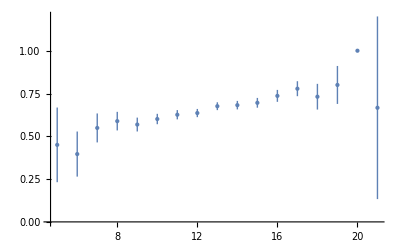

```mathematica
ListPlot[randomOutcomesMonFNRGtWald10000, PlotStyle->PointSize[Large]]
```

```mathematica
(* 100k samples randomly *) 
generateMonGtFNRvsCIOutcomesWald[100000]
```

```mathematica
randomOutcomesMonFNRGtWald100000 ={{3,0.200.200.35},{4,0.440.160.16},{5,0.480.080.08},{6,0.580.040.04},{7,0.5830.0250.025},{8,0.5970.0170.017},{9,0.5960.0120.012},{10,0.6150.0100.010},{11,0.6330.0080.008},{12,0.6500.0070.007},{13,0.6680.0070.007},{14,0.6810.0080.008},{15,0.6980.0090.009},{16,0.7170.0110.011},{17,0.7470.0150.015},{18,0.7740.0210.021},{19,0.760.040.04},{20,0.800.060.06},{21,0.870.100.10},{22,1.000000000000000001122},{23,1.000000000000000001122}};
```

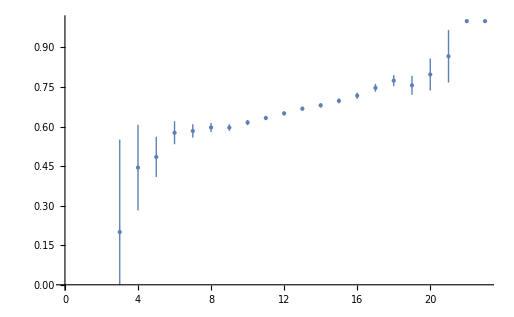

```mathematica
ListPlot[randomOutcomesMonFNRGtWald100000, PlotStyle->PointSize[Large]]
```

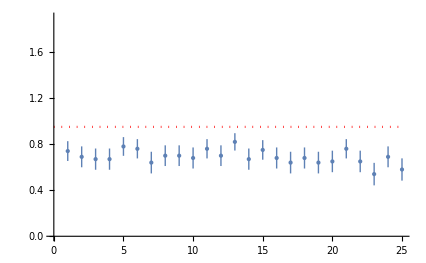
```mathematica
(*** MONITOR FNR WITH REPLACEMENT ***) 

monfnr100sampleChartData= {{1,0.740.090.09},{2,0.690.090.09},{3,0.670.090.09},{4,0.670.090.09},{5,0.780.080.08},{6,0.760.080.08},{7,0.640.090.09},{8,0.700.090.09},{9,0.700.090.09},{10,0.680.090.09},{11,0.760.080.08},{12,0.700.090.09},{13,0.820.080.08},{14,0.670.090.09},{15,0.750.080.08},{16,0.680.090.09},{17,0.640.090.09},{18,0.680.090.09},{19,0.640.090.09},{20,0.650.090.09},{21,0.760.080.08},{22,0.650.090.09},{23,0.540.100.10},{24,0.690.090.09},{25,0.580.100.10}};
Show[chart95conf[25],ListPlot[monfnr100sampleChartData, PlotStyle->PointSize[Medium]]]
-Graphics-
```

```mathematica
(** for fully disjoint partitions DET FPR -- too little data **) 
generatePartitionOutcomesForCharting[pairingGtDetFPR, {4,5}, 25, 10, interWald, interWilson]
```

{{1,0.830.170.09},{2,1.00000000000000000.200.0000000000000004},{3,1.000000000000000000.280.00000000000000011},{4,1.000000000000000000.350.00000000000000022},{5,10.40.},{6,1.000000000000000000.40.00000000000000022},{7,1.000000000000000000.50.00000000000000022},{8,1.000000000000000000.60.00000000000000022},{9,1.000000000000000000.60.00000000000000022},{10,1.000000000000000000.60.00000000000000022},{11,1.000000000000000000.70.00000000000000022},{12,1.000000000000000000.70.00000000000000022},{13,1.000000000000000000.70.00000000000000022},{14,1.000000000000000000.70.00000000000000022},{15,1.000000000000000000.70.00000000000000022},{16,1.000000000000000000.80.00000000000000022},{17,1.000000000000000000.80.00000000000000022},{18,1.000000000000000000.80.00000000000000022},{19,1.000000000000000000.80.00000000000000022},{20,1.000000000000000000.80.00000000000000022},{21,1.000000000000000000.80.00000000000000022},{22,1.000000000000000000.80.00000000000000022},{23,1.000000000000000000.80.00000000000000022},{24,1.000000000000000000.80.00000000000000022},{25,1.000000000000000000.80.00000000000000022}}